```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarF1[m_,s_]:=2-2Log[m]+(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
ScalarFPrime1[m_,s_]:=-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))(ArcTan[(√s)/(√(4 m^2-s))]-π);
PropagatorScalar[s_,M_,m_,c_]:=Abs[1+c×ScalarFPrime1[m,M^2]]/(s-M^2+c×(ScalarF0[m,s]-ScalarF1[m,M^2]));
```

```mathematica
NWA[p_,A_,B_,C_]:=C/((p^2-A)^2+B);
```

```mathematica
BestFit[m_,c_,Γ_]:=NMinimize[{Sum[((Abs[PropagatorScalar[p^2,1-ⅈ×Γ/2,m,c]]^2-NWA[p,A,B,C])^2)/(Abs[PropagatorScalar[p^2,1-ⅈ×Γ/2,m,c]]^2),{p,0.01,2,0.01}],A>0,B>0,C>0},{A,B,C},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->MachinePrecision][[2]];
```

```mathematica
Res1=BestFit[0.40001,0.04,0.3]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→0.974422,B→0.0730324,C→0.828043}

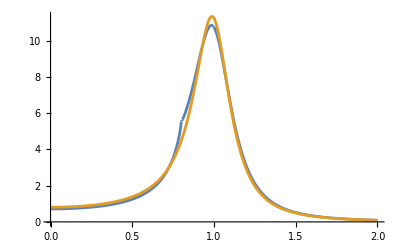

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.40001,0.04]]^2,NWA[p,A,B,C]/.Res1},{p,0,2}]
```

```mathematica
Res2=BestFit[0.45001,0.04,0.3]
```

{A→0.98663,B→0.0631996,C→0.715946}

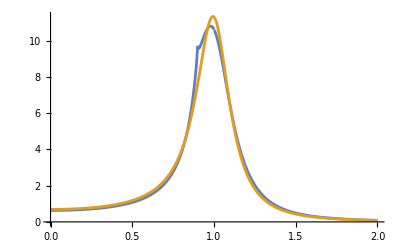

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.45001,0.04]]^2,NWA[p,A,B,C]/.Res2},{p,0,2}]
```

```mathematica
Res3=BestFit[0.50001,0.04,0.3]
```

{A→1.01886,B→0.0524983,C→0.596715}

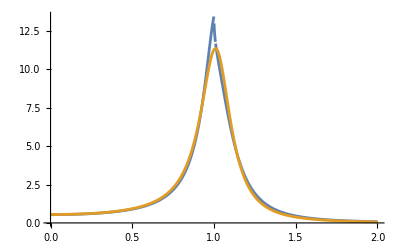

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.50001,0.04]]^2,NWA[p,A,B,C]/.Res3},{p,0,2},PlotRange->All]
```

```mathematica
Res4=BestFit[0.55001,0.04,0.3]
```

{A→1.07461,B→0.0485614,C→0.562285}

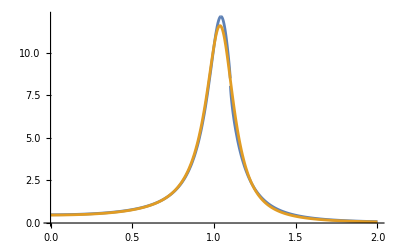

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.55001,0.04]]^2,NWA[p,A,B,C]/.Res4},{p,0,2},PlotRange->All]
```

```mathematica
Res5=BestFit[0.60001,0.04,0.3]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→1.12745,B→0.0496535,C→0.580781}

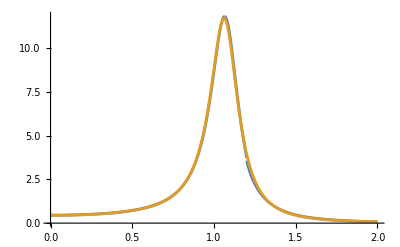

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1-ⅈ×0.3/2,0.60001,0.04]]^2,NWA[p,A,B,C]/.Res5},{p,0,2},PlotRange->All]
```